```mathematica
H[f]==-∫_a^b f[x]Log[f[x]]ⅆx
```

H[f]==-∫_a^b f[x] Log[f[x]]ⅆx

```mathematica
G[f]==∫_a^b f[x]ⅆx==1
```

G[f]==∫_a^b f[x]ⅆx==1

```mathematica
F[f]==∫_a^b L[x,f[x]]ⅆx==∫_a^b (-f[x]Log[f[x]]-λ f[x])ⅆx
```

F[f]==∫_a^b L[x,f[x]]ⅆx==∫_a^b (-λ f[x]-f[x] Log[f[x]])ⅆx

```mathematica
With[{L=(-f[x]Log[f[x]]-λ f[x])},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

(-1-λ-Log[f[x]])[x]==0

```mathematica
With[{L=Function[x,(-f[x]Log[f[x]]-λ f[x])]},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

-1-λ-Log[f[x]]==0

```mathematica
Reduce[-1-λ-Log[f[x]]==0]
```

λ==-1-Log[f[x]]

```mathematica
FindInstance[λ==-1-Log[f[x]],{x,λ}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[λ==-1-Log[f[x]],{x,λ}]

```mathematica
DSolve[-1-λ-Log[f[x]]==0,f[x],x]
```

{{f[x]→ⅇ^(-1-λ)}}

```mathematica
∫_a^b (ⅇ^(-1-λ))ⅆx
```

(-a+b) ⅇ^(-1-λ)

```mathematica
∫_a^b (ⅇ^(-1-λ))ⅆx==1
```

(-a+b) ⅇ^(-1-λ)==1

```mathematica
Solve[(-a+b) ⅇ^(-1-λ)==1, ⅇ^(-1-λ)]
```

Solve::ivar: ⅇ^(-1-λ) is not a valid variable.

Solve[(-a+b) ⅇ^(-1-λ)==1,ⅇ^(-1-λ)]

```mathematica
(-a+b) ==ⅇ^(-1-λ)
```

-a+b==ⅇ^(-1-λ)

```mathematica
1/(-a+b) ==ⅇ^(1+λ)
```

1/(-a+b)==ⅇ^(1+λ)

```mathematica
Log[1]
```

0

```mathematica
D[f[x],x]
```

f'[x]

```mathematica
f'[x]==λ f[x]
```

f'[x]==λ f[x]

```mathematica
DSolve[f'[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x λ) C[1]}}

```mathematica
Exp[f'[x]/f[x]]==λ f[x]
```

ⅇ^(f'[x]/f[x])==λ f[x]

```mathematica
DSolve[ⅇ^(f'[x]/f[x])==λ f[x],{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→(ⅇ^(ⅇ^(x+C[1])))/λ}}

```mathematica
With[{L={Identity,Identity}},
D[L,f[x]]-D[D[L,f'[x]],x]==0
]
```

{0,0}==0

```mathematica
With[{L={Identity,Exp}},
D[L,f[x]]-D[D[L,f'[x]],x]==0
]
```

{0,0}==0

```mathematica
With[{L={x,Exp[x]}},
D[L,f[x]]-D[D[L,f'[x]],x]==0
]
```

{0,0}==0

```mathematica
With[{L={x,f[x]}},
D[L,f[x]]-D[D[L,f'[x]],x]==0
]
```

{0,1}==0

```mathematica
∇_{x,y} f[x,y]
```

{f^(1,0)[x,y],f^(0,1)[x,y]}

```mathematica
∇_{x,y} f[x,y]==λ ∇_{x,y} g[x,y]
```

{f^(1,0)[x,y],f^(0,1)[x,y]}=={λ g^(1,0)[x,y],λ g^(0,1)[x,y]}

```mathematica
DSolve[{∇_{x,y} f[x,y]==λ ∇_{x,y} g[x,y],g[x,y]==0},f[x,y],{x,y}]
```

DSolve::deqx: Supplied equations are not differential or integral equations of the given functions.

DSolve[{{f^(1,0)[x,y],f^(0,1)[x,y]}=={λ g^(1,0)[x,y],λ g^(0,1)[x,y]},g[x,y]==0},f[x,y],{x,y}]

```mathematica
LetterCounts[ExampleData[{"Text","DonQuixoteIEnglish"}]]
```

<|e→97897,t→74644,a→65214,o→64951,h→56814,n→55138,i→51256,s→49736,r→44246,d→35268,l→29492,u→22141,m→20178,f→18638,w→18363,c→17272,y→14753,g→14690,b→11020,p→10880,v→8017,k→5381,I→3822,T→1774,x→1552,D→1538,A→1424,S→1395,H→894,C→891,Q→861,E→791,L→747,q→735,O→663,R→616,M→597,j→591,N→552,B→507,F→505,W→480,G→465,P→418,z→362,U→187,V→135,Y→124,X→112,Z→90,K→90,J→70|>

```mathematica
Keys[%27]
```

{e,t,a,o,h,n,i,s,r,d,l,u,m,f,w,c,y,g,b,p,v,k,I,T,x,D,A,S,H,C,Q,E,L,q,O,R,M,j,N,B,F,W,G,P,z,U,V,Y,X,Z,K,J}

```mathematica
Values[%27]
```

{97897,74644,65214,64951,56814,55138,51256,49736,44246,35268,29492,22141,20178,18638,18363,17272,14753,14690,11020,10880,8017,5381,3822,1774,1552,1538,1424,1395,894,891,861,791,747,735,663,616,597,591,552,507,505,480,465,418,362,187,135,124,112,90,90,70}

```mathematica
Map[Out[27],Out[29]]
```

{97897,74644,65214,64951,56814,55138,51256,49736,44246,35268,29492,22141,20178,18638,18363,17272,14753,14690,11020,10880,8017,5381,3822,1774,1552,1538,1424,1395,894,891,861,791,747,735,663,616,597,591,552,507,505,480,465,418,362,187,135,124,112,90,90,70}

```mathematica
Map[{#,Out[27][#]}&,Out[29]]
```

{{e,97897},{t,74644},{a,65214},{o,64951},{h,56814},{n,55138},{i,51256},{s,49736},{r,44246},{d,35268},{l,29492},{u,22141},{m,20178},{f,18638},{w,18363},{c,17272},{y,14753},{g,14690},{b,11020},{p,10880},{v,8017},{k,5381},{I,3822},{T,1774},{x,1552},{D,1538},{A,1424},{S,1395},{H,894},{C,891},{Q,861},{E,791},{L,747},{q,735},{O,663},{R,616},{M,597},{j,591},{N,552},{B,507},{F,505},{W,480},{G,465},{P,418},{z,362},{U,187},{V,135},{Y,124},{X,112},{Z,90},{K,90},{J,70}}

```mathematica
Normalize@Values[Out[27]]
```

{97897/(3 √4638640189),74644/(3 √4638640189),21738/(√4638640189),64951/(3 √4638640189),18938/(√4638640189),55138/(3 √4638640189),51256/(3 √4638640189),49736/(3 √4638640189),44246/(3 √4638640189),11756/(√4638640189),29492/(3 √4638640189),22141/(3 √4638640189),6726/(√4638640189),18638/(3 √4638640189),6121/(√4638640189),17272/(3 √4638640189),14753/(3 √4638640189),14690/(3 √4638640189),11020/(3 √4638640189),10880/(3 √4638640189),8017/(3 √4638640189),5381/(3 √4638640189),1274/(√4638640189),1774/(3 √4638640189),1552/(3 √4638640189),1538/(3 √4638640189),1424/(3 √4638640189),465/(√4638640189),298/(√4638640189),297/(√4638640189),287/(√4638640189),791/(3 √4638640189),249/(√4638640189),245/(√4638640189),221/(√4638640189),616/(3 √4638640189),199/(√4638640189),197/(√4638640189),184/(√4638640189),169/(√4638640189),505/(3 √4638640189),160/(√4638640189),155/(√4638640189),418/(3 √4638640189),362/(3 √4638640189),187/(3 √4638640189),45/(√4638640189),124/(3 √4638640189),112/(3 √4638640189),30/(√4638640189),30/(√4638640189),70/(3 √4638640189)}

```mathematica
Total@Out[33]
```

269659/(√4638640189)

```mathematica
N[269659/(√4638640189)]
```

3.95931

```mathematica
Standardize@Values[Out[27]]
```

{(329359 √(17/4320341373))/6,(236347 √(17/4320341373))/6,(66209 √(17/4320341373))/2,(197575 √(17/4320341373))/6,(55009 √(17/4320341373))/2,(158323 √(17/4320341373))/6,(142795 √(17/4320341373))/6,(136715 √(17/4320341373))/6,(114755 √(17/4320341373))/6,(26281 √(17/4320341373))/2,(55739 √(17/4320341373))/6,(26335 √(17/4320341373))/6,(6161 √(17/4320341373))/2,(12323 √(17/4320341373))/6,(1247 √(51/1440113791))/2,(6859 √(17/4320341373))/6,-(3217 √(17/4320341373))/6,-(3469 √(17/4320341373))/6,-(18149 √(17/4320341373))/6,-(18709 √(17/4320341373))/6,-(30161 √(17/4320341373))/6,-(40705 √(17/4320341373))/6,-(15647 √(17/4320341373))/2,-(55133 √(17/4320341373))/6,-(56021 √(17/4320341373))/6,-(56077 √(17/4320341373))/6,-(56533 √(17/4320341373))/6,-(18883 √(17/4320341373))/2,-(6517 √(51/1440113791))/2,-(19555 √(17/4320341373))/2,-(19595 √(17/4320341373))/2,-(59065 √(17/4320341373))/6,-(19747 √(17/4320341373))/2,-(19763 √(17/4320341373))/2,-(19859 √(17/4320341373))/2,-(59765 √(17/4320341373))/6,-(6649 √(51/1440113791))/2,-(19955 √(17/4320341373))/2,-(6669 √(51/1440113791))/2,-(6689 √(51/1440113791))/2,-(60209 √(17/4320341373))/6,-(6701 √(51/1440113791))/2,-(20123 √(17/4320341373))/2,-(60557 √(17/4320341373))/6,-(60781 √(17/4320341373))/6,-(61481 √(17/4320341373))/6,-(20563 √(17/4320341373))/2,-(61733 √(17/4320341373))/6,-(61781 √(17/4320341373))/6,-(20623 √(17/4320341373))/2,-(20623 √(17/4320341373))/2,-(61949 √(17/4320341373))/6}

```mathematica
Total@Out[36]
```

0

```mathematica
Normalize@Out[28]
```

{97897/(3 √4638640189),74644/(3 √4638640189),21738/(√4638640189),64951/(3 √4638640189),18938/(√4638640189),55138/(3 √4638640189),51256/(3 √4638640189),49736/(3 √4638640189),44246/(3 √4638640189),11756/(√4638640189),29492/(3 √4638640189),22141/(3 √4638640189),6726/(√4638640189),18638/(3 √4638640189),6121/(√4638640189),17272/(3 √4638640189),14753/(3 √4638640189),14690/(3 √4638640189),11020/(3 √4638640189),10880/(3 √4638640189),8017/(3 √4638640189),5381/(3 √4638640189),1274/(√4638640189),1774/(3 √4638640189),1552/(3 √4638640189),1538/(3 √4638640189),1424/(3 √4638640189),465/(√4638640189),298/(√4638640189),297/(√4638640189),287/(√4638640189),791/(3 √4638640189),249/(√4638640189),245/(√4638640189),221/(√4638640189),616/(3 √4638640189),199/(√4638640189),197/(√4638640189),184/(√4638640189),169/(√4638640189),505/(3 √4638640189),160/(√4638640189),155/(√4638640189),418/(3 √4638640189),362/(3 √4638640189),187/(3 √4638640189),45/(√4638640189),124/(3 √4638640189),112/(3 √4638640189),30/(√4638640189),30/(√4638640189),70/(3 √4638640189)}

```mathematica
Total@Out@39
```

269659/(√4638640189)

```mathematica
N[269659/(√4638640189)]
```

3.95931

```mathematica
Map[#^(Length@Out[28])&,Out[28]]
```

{33113716866108671939450398399095980631190637355105169068761780827257521063994441937352534667268261660147364284342314901071679979272228700142644707168679174501762926621106678083960638862141557689568746301934452471070006184665976582804744898585464514064535444641,24873392242172624588093378069652631067912196299750152819853354095802913100772056259527476135684133632560175238149212839646759739866919107277154765298293090810216675518144872855360033757037217892661086743091556875224441953444873905783920220427171435380736,22167853116793400074462377854801437399568237953061854723368125244272963801748365426289633164575071367859953219651705262640641541327537069224889173404376294479220903034796368865462180175795534457594413971859067814174101199470828462778012761606687031296,17966512406708326456805819839985091405813366087980162165069040229455260642067272810594024273999248332349111452224669172607783138252373155797624553222848299948247229455022431753151055490917039547209814003455045950217259895421648708231745222069256442401,17048221551610017751708464253458051155731593076620735745406072262973362246934999398123718239138481736748941797685905053921346751325979075870289428756895397816199239096620286321820757993660934069007253896848690422026800880302741236997176261760516096,3592960732616542021048782502152851878354553910131935442076035340511471317064864419369367427044393596363342070637297799831604573330659950013715583074784263481789150412738590191206106754062754331522064711729233860086965521414118666361996113614995456,80672398845127045468461322359520083682215842411318158686731837538673861405990137042510743400053841932883581058618265838642319717445033913584498677115832279064063396918349019690604794952207748038475185617409013810370333515939276287733116788801536,16861042641659073432616605922751982228161355065932718433186762564648957647997244904315041871378415669972209039806391534215513031874604050340567921362080429115293642387791014303180688027995112222385977438213992255472678174417722110999909625757696,38498940701385839776651569902947970000493421837043597318504407978030600257854217248289785246189492830519458556888242990942413617726009201385686012665252248802959110169444223488722584872927781202286261803510901464335415105912510816342314582016,290939889968756684970056502547044614246543341330354332788904629365670036068138730612486662370795462525033384254946905149067957016688282752744251607918520998427906343335035597401307078856312315156598872288284674244216646024026787913138176,26583962277843733003900287599840322535952056991604087091573871067220797693692950889356311362462416540187613132923193436855088646944992123095585518693371552407810640466150933405018742145657653022706711856257098044793728266146662055936,8917765753118549587610450281491798336871985451233359982925069559819842561608746922091568315922011969451177019585398071678159772838244432807929088876450630100557332494196275742689487315219966218401226469143346081217583521700881,71394066644450021772675765154518719210579839208323276401325185277589871046866903765746619455427833427827948709019652545662778457777456145345094189711794127132111550792511666138310656684148999580564353845290196744976063266816,1150175161694112010885066394712729808009405613954903484046923271566404441975114364232850006237609650840434079233664846831601808446424483734707377031230357283053605480517427156221892978599197755819778007791723321946806419456,530968771777842333623236931793757776922611412158147673867381123798459993120406995198574988019687955381385888461261519899587340411326559066139635705580731973251851860564164542532787294541188497140070500416450812445937698481,21969325575927304500343146073419515275399846491607231306976958768328961178329980183853499126130829088151540779448400457117736078229665770548079191761899839467660379710491795960830131063265395936182156804602296351395414016,6050312484258690062604021707202260151894186870625310866963727120173681984355915298577505260192498308974546915458461897711085504554122339095152319481614665416512923792953253321714980370202699071580054511890820716506241,4843210900761415220770333569827360563573470498610820774803800017788130897112552766147239508042311349146449735317958861936220706377801735029963716329583533918022269610000000000000000000000000000000000000000000000000000,1561143822298449173601283297780635799466627175901156811033292115461853360443144361841890733636867080408547002600905859778840539306690706941903933220301265960960000000000000000000000000000000000000000000000000000,802975988733670008539142622182203012349005302104883974706621731724743102098539164015838415863936074393002989453620664656102024894586533075500367255154783682560000000000000000000000000000000000000000000000000000,102004174858331250244601286348018162966224458934915589047700043836886916035985330647919621009229939064051119431250119623061473737471673370282314721065894629049584180559590778488243621262464139774574352961,101128970570503808230116231602960491681830082705992145480366743546859107813284634666424197493729220643610402006105170264142378567222419984379708488864731597435954890495776588235634936167495754161,1901583942301364923845603214186345408343374257592634781882290698908164326003147006004935443742254688182905278211894789205094864115992713265255997695349032795941218650978143465387973410816,8822425623535871702805917131017442580414715462884301374579077603893328562305451407013655077310047758228745258970009842332640678339226774285274704552438496514880701464576,8440521490111669202097279918098382885335913379141860424363650872229989603789963979485112851125609612693105340147289900245284467463126531040132515779425569242974519296,5269015112388095495744705157451767855016077627117944089983859425672298728826346323914072554480338750788568781127863472973694896681390904805997373878806121874829869056,96054882181323139825568485804033841328574536022167937768527155643391774317474771254806211841711552612607915352028575315023693107496843255032538350017403324806987776,32950256197141387296860607102815806555886083859317611118865529424156636526200685135522838566269642708035485419665787051474712046061910086791613139212131500244140625,2948159510591670063417123808781823215426727360994941294082023640612134381731915475457007941472679960101831359890923663748899214136443435913225101153140736,2475372773891775457964237033383513215293353015687554552257925046687728646800915426907715031001941789939768943807608279148431746912152456722332545236520881,417026713598875508333870991662487480645453452919898490662500035438048063512907951688762161527791817276861087927225003032191951951695765437401839950354321,5071975439793272560764068626125949508909730835094587838616813188997306939969102003317112290004840111762968802373190704620747910107485852181832600747681,258625470883124156776741381976185882770124939161066492328530735899970953443901070160072615569240701531062029211937079313481607504969339758033371424241,111414478646298879291091347168172797678040788050528133992930738130571798113418879949078629746791692700025817087985391395932310842908918857574462890625,523243060283912327432850744880912095882134742530796960616331482742740569076876685992802465472938226040404162003868458187236778420612879816560363681,11433969582841095674787854084600380088897430487181104284753077631230840162414878017891772431063579772756046736536303389463666919879521102731411456,2242152866167428091107182383841205739384687619847126097493214855799959416808662404919938817445402461603203863568126920855525691144175881666265841,1326016737157226178576786924529358736274763186683219836913612932025920308925900726989267796795877599385132829874914085760345401106565210528761281,38091847933867042835455747431681251920017839451670464688413654908289889072095484121347849107093947701279718855878617740076595838148736551223296,457524005127552359778097700683398546421314539215016626248048421643922994057664647680256605108551885516868104626989751685994323730820884129201,372521773753341262327499054618996583385054343016912477623135723456402756086336064269960078957787648657353773984368672245182096958160400390625,26579349234869996652552191374272260963030470744846773822896129328985247481426529442856960000000000000000000000000000000000000000000000000000,5099804763670191230286251395887157393867532355841858157360476017058753109093768024505211671947812107854591801014976226724684238433837890625,20006294260978676475008000365130465291371246612136720031643345240284891613764319020690294668531146240588313847231263247401700051990347776,11293944981135402883753540669480913750883769107103736181013345534354650414755190157018010782275817973828964840570035937027532527763456,13669843416505250390024437923941146918829216445879544618814902349211167973656112300983050370860812638913058997545583281,598902273531115721421318177436014748264845076040314815005215346366217396048003962505390518344938755035400390625,7209873226301130434681615382902273493671709286272727005104085866014011564757548332857862885304434337960165376,36252434692275124905339915405331540026346382668310265891823415517226698567886683190896443581379100547219456,417455791792929178139533515110153230888707092820810000000000000000000000000000000000000000000000000000,417455791792929178139533515110153230888707092820810000000000000000000000000000000000000000000000000000,881247870897231951843937366879128181133112010000000000000000000000000000000000000000000000000000}

```mathematica
Map[#^(Length@Out[28])&,Out[28]]^(1/(Length@Out[28]))
```

{97897,74644,65214,64951,56814,55138,51256,49736,44246,35268,29492,22141,20178,18638,18363,17272,14753,14690,11020,10880,8017,5381,3822,1774,1552,1538,1424,1395,894,891,861,791,747,735,663,616,597,591,552,507,505,480,465,418,362,187,135,124,112,90,90,70}

```mathematica
(Total@Map[#^(Length@Out[28])&,Out[28]])^(1/(Length@Out[28]))
```

33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52)

```mathematica
Map[#/Out[46]&,Out[28]]
```

{97897/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),74644/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(21738 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),64951/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(18938 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),55138/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),51256/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),49736/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),44246/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(11756 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),29492/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),22141/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(6726 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),18638/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(6121 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),17272/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),14753/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(2938 5^(51/52))/6622748355931203677960331607498737221067068825341422840248370238968841978462142788295585037883060872995694052040550572003422479017873913528460378639298682215739677493455891470206262572108500476056616428799789042998632491401038929475754469416635367202908527121^(1/52),(2204 5^(51/52))/6622748355931203677960331607498737221067068825341422840248370238968841978462142788295585037883060872995694052040550572003422479017873913528460378639298682215739677493455891470206262572108500476056616428799789042998632491401038929475754469416635367202908527121^(1/52),(2176 5^(51/52))/6622748355931203677960331607498737221067068825341422840248370238968841978462142788295585037883060872995694052040550572003422479017873913528460378639298682215739677493455891470206262572108500476056616428799789042998632491401038929475754469416635367202908527121^(1/52),8017/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),5381/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(1274 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),1774/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),1552/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),1538/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),1424/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(93 15^(51/52))/2207582785310401225986777202499579073689022941780474280082790079656280659487380929431861679294353624331898017346850190667807493005957971176153459546432894071913225831151963823402087524036166825352205476266596347666210830467012976491918156472211789067636175707^(1/52),(298 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),(297 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),(287 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),791/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(249 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),(49 15^(51/52))/2207582785310401225986777202499579073689022941780474280082790079656280659487380929431861679294353624331898017346850190667807493005957971176153459546432894071913225831151963823402087524036166825352205476266596347666210830467012976491918156472211789067636175707^(1/52),(221 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),616/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(199 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),(197 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),(184 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),(169 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52),(101 5^(51/52))/6622748355931203677960331607498737221067068825341422840248370238968841978462142788295585037883060872995694052040550572003422479017873913528460378639298682215739677493455891470206262572108500476056616428799789042998632491401038929475754469416635367202908527121^(1/52),(32 15^(51/52))/2207582785310401225986777202499579073689022941780474280082790079656280659487380929431861679294353624331898017346850190667807493005957971176153459546432894071913225831151963823402087524036166825352205476266596347666210830467012976491918156472211789067636175707^(1/52),(31 15^(51/52))/2207582785310401225986777202499579073689022941780474280082790079656280659487380929431861679294353624331898017346850190667807493005957971176153459546432894071913225831151963823402087524036166825352205476266596347666210830467012976491918156472211789067636175707^(1/52),418/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),362/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),187/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(9 15^(51/52))/2207582785310401225986777202499579073689022941780474280082790079656280659487380929431861679294353624331898017346850190667807493005957971176153459546432894071913225831151963823402087524036166825352205476266596347666210830467012976491918156472211789067636175707^(1/52),124/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),112/33113741779656018389801658037493686105335344126707114201241851194844209892310713941477925189415304364978470260202752860017112395089369567642301893196493411078698387467279457351031312860542502380283082143998945214993162457005194647378772347083176836014542635605^(1/52),(6 15^(51/52))/2207582785310401225986777202499579073689022941780474280082790079656280659487380929431861679294353624331898017346850190667807493005957971176153459546432894071913225831151963823402087524036166825352205476266596347666210830467012976491918156472211789067636175707^(1/52),(6 15^(51/52))/2207582785310401225986777202499579073689022941780474280082790079656280659487380929431861679294353624331898017346850190667807493005957971176153459546432894071913225831151963823402087524036166825352205476266596347666210830467012976491918156472211789067636175707^(1/52),(14 5^(51/52))/6622748355931203677960331607498737221067068825341422840248370238968841978462142788295585037883060872995694052040550572003422479017873913528460378639298682215739677493455891470206262572108500476056616428799789042998632491401038929475754469416635367202908527121^(1/52)}

```mathematica
Total@Out[47]
```

(40201 15^(51/52))/2207582785310401225986777202499579073689022941780474280082790079656280659487380929431861679294353624331898017346850190667807493005957971176153459546432894071913225831151963823402087524036166825352205476266596347666210830467012976491918156472211789067636175707^(1/52)+(68654 3^(51/52))/11037913926552006129933886012497895368445114708902371400413950398281403297436904647159308396471768121659490086734250953339037465029789855880767297732164470359566129155759819117010437620180834126761027381332981738331054152335064882459590782361058945338180878535^(1/52)

```mathematica
N@Out@48
```

8.26355

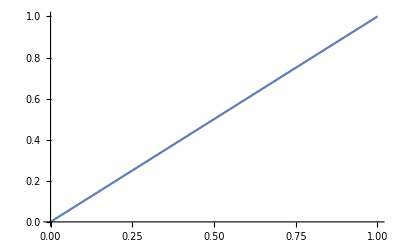

```mathematica
Plot[x,{x,0,1}]
```

```mathematica
∫_0^1 f[x]ⅆx
```

∫_0^1 f[x]ⅆx

```mathematica
(∫_a^b f[x]ⅆx)/(b-a)
```

(∫_a^b f[x]ⅆx)/(-a+b)

```mathematica
With[{f=Identity,a=0,b=1},
(∫_a^b f[x]ⅆx)/(-a+b)
]
```

1/2

```mathematica
With[{f=Identity,a=0,b=1},
∫_a^b f[x]ⅆx
]
```

1/2

```mathematica
With[{f=Identity,a=0,b=1},
(∫_a^b f[x]ⅆx)/2
]
```

1/4

```mathematica
1==∫_0^a xⅆx
```

1==a^2/2

```mathematica
Reduce[1==a^2/2]
```

a==-√2||a==√2

```mathematica
FullSimplify[
Reduce[1==∫_0^a xⅆx,a,],
a∈]
```

a==√2

```mathematica
PositiveReals
```

```mathematica
With[{f=Identity,a=0,b=1},
(∫_a^b f[x]ⅆx)/2
]
```

1/4

```mathematica
∫_0^(1/4) xⅆx
```

1/32

```mathematica
With[{f=Identity,a=0,b=1},
(∫_a^b f[x]ⅆx)/2==∫_0^c f[x]ⅆx
]
```

1/4==c^2/2

```mathematica
Reduce[1/4==c^2/2]
```

c==-1/(√2)||c==1/(√2)

```mathematica
With[{f=Identity,a=0,b=1},
Reduce[(∫_a^b f[x]ⅆx)/2==∫_0^c f[x]ⅆx,c,]
]
```

c==1/(√2)

```mathematica
PositiveReals
```

```mathematica
∫_0^(2^(-1/2)) xⅆx
```

1/4

```mathematica
∫_0^(2^(-1/2)) xⅆx
```

```mathematica
With[{f=Identity,a=0,b=1},
∫_a^b f[x]ⅆx==∫_0^(2^(-1/2)) xⅆx+∫_(2^(-1/2))^1 xⅆx
]
```

True

```mathematica
With[{f=Identity,a=0,b=1},
Reduce[(∫_a^b f[x]ⅆx)/2==∫_0^c f[x]ⅆx==∫_c^b f[x]ⅆx,c,]
]
```

c==1/(√2)

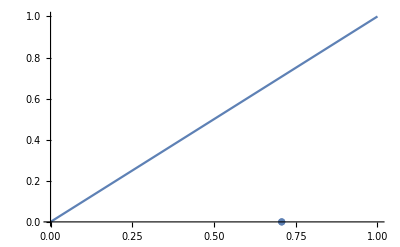

```mathematica
Show[{
Plot[x,{x,0,1}],
ListPlot[{{1/(√2),0}}]
}]
```

```mathematica
With[{f=Sqrt,a=0,b=1},
Reduce[(∫_a^b f[x]ⅆx)/2==∫_0^c f[x]ⅆx==∫_c^b f[x]ⅆx,c,]
]
```

c==1/2^(2/3)

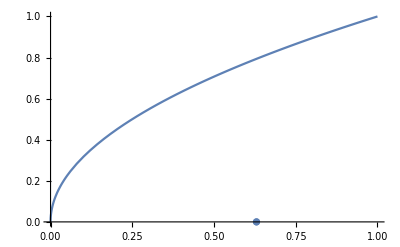

```mathematica
Show[{
Plot[Sqrt[x],{x,0,1}],
ListPlot[{{1/2^(2/3),0}}]
}]
```

```mathematica
a Sum[Subscript[x, i],{i,1,n}]
```

a ∑_(i=1)^n x_i

```mathematica
RotationMatrix[θ]
```

{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}

```mathematica
RotationMatrix[θ,{x,f[x],0}]
```

{{(x Conjugate[x] Conjugate[1/(√(Abs[x]^2+Abs[f[x]]^2) √(x Conjugate[x]+Conjugate[f[x]] f[x]))] (x^2 Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))]+Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x]^2) (Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))+Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))))/(√(Abs[x]^2+Abs[f[x]]^2) √(x Conjugate[x]+Conjugate[f[x]] f[x]))+(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] ((Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ] f[x])/(x Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))-(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] Sin[θ])/(x √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(x Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))-(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] (-(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ] f[x])/(x √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))-(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] Sin[θ])/(x Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x]))),(Conjugate[x] Conjugate[1/(√(Abs[x]^2+Abs[f[x]]^2) √(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x] (x^2 Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))]+Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x]^2) (Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))+Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))))/(√(Abs[x]^2+Abs[f[x]]^2) √(x Conjugate[x]+Conjugate[f[x]] f[x]))-(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] ((Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ] f[x])/(x Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))-(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] Sin[θ])/(x √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(x √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))+(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] (-(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ] f[x])/(x √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))-(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] Sin[θ])/(x Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x]))),(Conjugate[x/(√(Abs[x]^2+Abs[f[x]]^2))] (-x^2 Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))]-Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x]^2) ((Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ] f[x])/(x Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))-(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] Sin[θ])/(x √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))+(Conjugate[f[x]/(√(Abs[x]^2+Abs[f[x]]^2))] (-x^2 Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))]-Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x]^2) (-(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ] f[x])/(x √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))-(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] Sin[θ])/(x Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))},{(x Conjugate[f[x]] Conjugate[1/(√(Abs[x]^2+Abs[f[x]]^2) √(x Conjugate[x]+Conjugate[f[x]] f[x]))] (x^2 Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))]+Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x]^2) (Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))+Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))))/(√(Abs[x]^2+Abs[f[x]]^2) √(x Conjugate[x]+Conjugate[f[x]] f[x]))+(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] (-(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ])/(Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))+(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Sin[θ])/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(x Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))-(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] ((Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ])/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))+(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Sin[θ])/(Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x]))),(Conjugate[f[x]] Conjugate[1/(√(Abs[x]^2+Abs[f[x]]^2) √(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x] (x^2 Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))]+Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x]^2) (Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))+Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))))/(√(Abs[x]^2+Abs[f[x]]^2) √(x Conjugate[x]+Conjugate[f[x]] f[x]))-(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] (-(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ])/(Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))+(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Sin[θ])/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(x √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))+(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] ((Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ])/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))+(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Sin[θ])/(Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x]))),(Conjugate[x/(√(Abs[x]^2+Abs[f[x]]^2))] (-x^2 Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))]-Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x]^2) (-(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ])/(Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))+(Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Sin[θ])/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))+(Conjugate[f[x]/(√(Abs[x]^2+Abs[f[x]]^2))] (-x^2 Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))]-Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x]^2) ((Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Cos[θ])/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))+(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] Sin[θ])/(Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))))/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))},{-((Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] ((Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] Cos[θ] f[x] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))))/(√(Abs[x]^2+Abs[f[x]]^2))-(x Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))) Sin[θ])/(√(Abs[x]^2+Abs[f[x]]^2))))/(Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x]))))+(Conjugate[f[x]/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] ((x Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] Cos[θ] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))))/(√(Abs[x]^2+Abs[f[x]]^2))+(Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))) Sin[θ])/(√(Abs[x]^2+Abs[f[x]]^2))))/(x Conjugate[x] √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x]))),1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] ((Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] Cos[θ] f[x] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))))/(√(Abs[x]^2+Abs[f[x]]^2))-(x Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))) Sin[θ])/(√(Abs[x]^2+Abs[f[x]]^2)))-1/(x √((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))Conjugate[1/(√((x Conjugate[x]+Conjugate[f[x]] f[x])/(x Conjugate[x])))] f[x] ((x Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] Cos[θ] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))))/(√(Abs[x]^2+Abs[f[x]]^2))+(Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))) Sin[θ])/(√(Abs[x]^2+Abs[f[x]]^2))),(Conjugate[f[x]/(√(Abs[x]^2+Abs[f[x]]^2))] (-x^2 Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))]-Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x]^2) ((Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] Cos[θ] f[x] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))))/(√(Abs[x]^2+Abs[f[x]]^2))-(x Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))) Sin[θ])/(√(Abs[x]^2+Abs[f[x]]^2))))/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))+(Conjugate[x/(√(Abs[x]^2+Abs[f[x]]^2))] (-x^2 Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))]-Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x]^2) ((x Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] Cos[θ] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))))/(√(Abs[x]^2+Abs[f[x]]^2))+(Conjugate[1/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))] f[x] (-Conjugate[x]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))-Conjugate[f[x]]^2/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))) Sin[θ])/(√(Abs[x]^2+Abs[f[x]]^2))))/(√(x Conjugate[x]+Conjugate[f[x]] f[x]))}}

```mathematica
FullSimplify[RotationMatrix[θ,{x,f[x],0}],θ∈∧{x,f[x]}∈Reals∧0≤θ≤2π]
```

{{(x^2+Cos[θ] f[x]^2)/(x^2+f[x]^2),-(x (-1+Cos[θ]) f[x])/(x^2+f[x]^2),(f[x] Sin[θ])/(√(x^2+f[x]^2))},{-(x (-1+Cos[θ]) f[x])/(x^2+f[x]^2),(x^2 Cos[θ]+f[x]^2)/(x^2+f[x]^2),-(x Sin[θ])/(√(x^2+f[x]^2))},{-(f[x] Sin[θ])/(√(x^2+f[x]^2)),(x Sin[θ])/(√(x^2+f[x]^2)),Cos[θ]}}

```mathematica
PositiveReals
```

```mathematica
FullSimplify[RotationMatrix[θ,{x,1,0}],θ∈∧{x,f[x]}∈Reals∧0≤θ≤2π]
```

{{(x^2+Cos[θ])/(1+x^2),(x-x Cos[θ])/(1+x^2),Sin[θ]/(√(1+x^2))},{(x-x Cos[θ])/(1+x^2),(1+x^2 Cos[θ])/(1+x^2),-(x Sin[θ])/(√(1+x^2))},{-Sin[θ]/(√(1+x^2)),(x Sin[θ])/(√(1+x^2)),Cos[θ]}}

```mathematica
FullSimplify[RotationMatrix[θ,{1,1,0}],θ∈∧{x,f[x]}∈Reals∧0≤θ≤2π]
```

{{Cos[θ/2]^2,Sin[θ/2]^2,Sin[θ]/(√2)},{Sin[θ/2]^2,Cos[θ/2]^2,-Sin[θ]/(√2)},{-Sin[θ]/(√2),Sin[θ]/(√2),Cos[θ]}}

```mathematica
FullSimplify[RotationMatrix[π/2,{1,1,0}],θ∈∧{x,f[x]}∈Reals∧0≤θ≤2π]
```

{{1/2,1/2,1/(√2)},{1/2,1/2,-1/(√2)},{-1/(√2),1/(√2),0}}

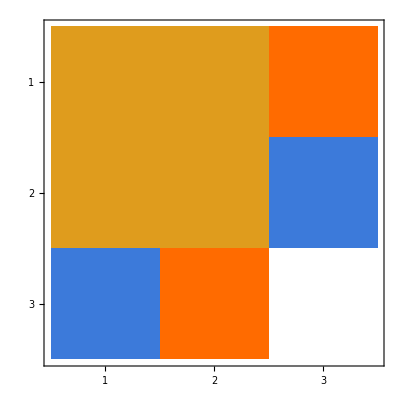

```mathematica
MatrixPlot[{{1/2,1/2,1/(√2)},{1/2,1/2,-1/(√2)},{-1/(√2),1/(√2),0}}]
```

```mathematica
{{1/2,1/2,1/(√2)},{1/2,1/2,-1/(√2)},{-1/(√2),1/(√2),0}}.{x,x,0}
```

{x,x,0}

```mathematica
FullSimplify[RotationMatrix[θ,{x,f[x],0}],θ∈∧{x,f[x]}∈Reals∧0≤θ≤2π]/.{f[x]->x}
```

{{(x^2+x^2 Cos[θ])/(2 x^2),1/2 (1-Cos[θ]),(x Sin[θ])/(√2 √(x^2))},{1/2 (1-Cos[θ]),(x^2+x^2 Cos[θ])/(2 x^2),-(x Sin[θ])/(√2 √(x^2))},{-(x Sin[θ])/(√2 √(x^2)),(x Sin[θ])/(√2 √(x^2)),Cos[θ]}}

```mathematica
FullSimplify[RotationMatrix[θ,{x,f[x],0}],θ∈∧{x,f[x]}∈Reals∧0≤θ≤2π]/.{f[x]->x,θ->π/2}
```

{{1/2,1/2,x/(√2 √(x^2))},{1/2,1/2,-x/(√2 √(x^2))},{-x/(√2 √(x^2)),x/(√2 √(x^2)),0}}

```mathematica
MatrixForm[{{1/2,1/2,x/(√2 √(x^2))},{1/2,1/2,-x/(√2 √(x^2))},{-x/(√2 √(x^2)),x/(√2 √(x^2)),0}}]
```

(1/2 | 1/2 | x/(√2 √(x^2))
1/2 | 1/2 | -x/(√2 √(x^2))
-x/(√2 √(x^2)) | x/(√2 √(x^2)) | 0)

```mathematica
Eigenvalues[{{1/2,1/2,x/(√2 √(x^2))},{1/2,1/2,-x/(√2 √(x^2))},{-x/(√2 √(x^2)),x/(√2 √(x^2)),0}}]
```

{Root[-8 (x^2)^(3/2)+4 x^2 #1-2 √(x^2) #1^2+#1^3&,1]/(2 √(x^2)),Root[-8 (x^2)^(3/2)+4 x^2 #1-2 √(x^2) #1^2+#1^3&,2]/(2 √(x^2)),Root[-8 (x^2)^(3/2)+4 x^2 #1-2 √(x^2) #1^2+#1^3&,3]/(2 √(x^2))}

```mathematica
Det[{{1/2,1/2,x/(√2 √(x^2))},{1/2,1/2,-x/(√2 √(x^2))},{-x/(√2 √(x^2)),x/(√2 √(x^2)),0}}]
```

1

```mathematica
{{1/2,1/2,1/(√2)},{1/2,1/2,-1/(√2)},{-1/(√2),1/(√2),0}}.{x,x,0}
```

{x,x,0}

```mathematica
J[{a_Real,b_Real}]:={-b,a}
```

```mathematica
J[{x,f[x]}]
```

J[{x,f[x]}]

```mathematica
ClearAll[J]
```

```mathematica
J[{a_,b_}]:={-b,a}
```

```mathematica
J[{x,f[x]}]
```

{-f[x],x}

```mathematica
FullSimplify[
({x''[t],y''[t]}.J[{x'[t],y'[t]}])/Norm[{x'[t],y'[t]}]^3
,{x,f[x]}∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/((Abs[x'[t]]^2+Abs[y'[t]]^2)^(3/2))

```mathematica
FullSimplify[
({x''[t],y''[t]}.J[{x'[t],y'[t]}])/Norm[{x'[t],y'[t]}]^3
,{x,x[t],y[t],x'[t],y'[t],x''[t],y''[t]}∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))

```mathematica
FullSimplify[
({x''[t],y''[t]}.J[{x'[t],y'[t]}])/Norm[{x'[t],y'[t]}]^3==0
,{x,x[t],y[t],x'[t],y'[t],x''[t],y''[t]}∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^2+y'[t]^2))==0

```mathematica
DSolve[(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^2+y'[t]^2))==0,{x[t],y[t],x[t],y[t]},{t}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^2+y'[t]^2))==0,{x[t],y[t],x[t],y[t]},{t}]

```mathematica
With[{x=Identity},
FullSimplify[
({x''[t],y''[t]}.J[{x'[t],y'[t]}])/Norm[{x'[t],y'[t]}]^3==0
,{x,x[t],y[t],x'[t],y'[t],x''[t],y''[t]}∈Reals]
]
```

y''[t]==0

```mathematica
DSolve[y''[t]==0,{y[t]},{t}]
```

{{y[t]→C[1]+t C[2]}}

```mathematica
With[{x=Identity},
FullSimplify[
({x''[t],y''[t]}.J[{x'[t],y'[t]}])/Norm[{x'[t],y'[t]}]^3==1
,{x,x[t],y[t],x'[t],y'[t],x''[t],y''[t]}∈Reals]
]
```

(1+y'[t]^2)^(3/2)==y''[t]

```mathematica
DSolve[(1+y'[t]^2)^(3/2)==y''[t],{y[t],y[t]},{t}]
```

{{y[t]→-ⅈ √(-1+t^2+2 t C[1]+C[1]^2)+C[2]},{y[t]→ⅈ √(-1+t^2+2 t C[1]+C[1]^2)+C[2]}}

```mathematica
With[{x=Identity},
FullSimplify[
({x''[t],y''[t]}.J[{x'[t],y'[t]}])/Norm[{x'[t],y'[t]}]^3==2
,{x,x[t],y[t],x'[t],y'[t],x''[t],y''[t]}∈Reals]
]
```

2 (1+y'[t]^2)^(3/2)==y''[t]

```mathematica
DSolve[2 (1+y'[t]^2)^(3/2)==y''[t],{y[t],y[t]},{t}]
```

{{y[t]→-1/2 ⅈ √(-1+4 t^2+4 t C[1]+C[1]^2)+C[2]},{y[t]→1/2 ⅈ √(-1+4 t^2+4 t C[1]+C[1]^2)+C[2]}}

```mathematica
With[{x=Identity},
FullSimplify[
({x''[t],y''[t]}.J[{x'[t],y'[t]}])/Norm[{x'[t],y'[t]}]^3==3
,{x,x[t],y[t],x'[t],y'[t],x''[t],y''[t]}∈Reals]
]
```

3 (1+y'[t]^2)^(3/2)==y''[t]

```mathematica
1/2 ⅈ √(-1+4 t^2+4 t C[1]+C[1]^2)+C[2]/.{C[2]->0,C[1]->1}
```

1/2 ⅈ √(4 t+4 t^2)

```mathematica
InverseLaplaceTransform[1/2 ⅈ √(4 t+4 t^2),t,x]
```

1/2 ⅈ InverseLaplaceTransform[√(4 t+4 t^2),t,x]

```mathematica
LaplaceTransform[1/2 ⅈ √(4 t+4 t^2),t,x]
```

(ⅈ ⅇ^(x/2) BesselK[1,x/2])/(2 x)

```mathematica
{x,f[x]} x {x,f[x]}
```

{x^3,x f[x]^2}

```mathematica
Cross[{x,f[x]},{x,f[x]}]
```

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

{x,f[x]}×{x,f[x]}

```mathematica
Cross[a,b]
```

a×b

```mathematica
Cross[{a,b,c},{a,b,c}]
```

{0,0,0}

```mathematica
Cross[{a,b,0},{a,b,0}]
```

{0,0,0}

```mathematica
Cross[{a,b,0},{b,a,0}]
```

{0,0,a^2-b^2}

```mathematica
Cross[{x,f[x],0},{x,f[x],0}]
```

{0,0,0}

```mathematica
Cross[{x,f[x],0},{-x,-f[x],0}]
```

{0,0,0}